```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

# Neural Logic Networks

Working repo: https://github.com/github/neural-logic

## A classification problem

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

### Feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],Sequence@@Normal[Drop[Normal[encoders],-1]]
];
```

## A standard neural network

### Define net

```mathematica
standardNet=NetChain[{LinearLayer[20,"Input"->inputSize],ElementwiseLayer["ScaledExponentialLinearUnit"],LinearLayer[4],SoftmaxLayer[]}]
```

NetChain[<>]

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->standardNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->CrossEntropyLossLayer["Probabilities"]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

```mathematica
NetFlatten[trainableNet]
```

NetGraph[<>]

### Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"];
```

```mathematica
result
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:13225  rounds:529  time:39s  examples/s:22066
data | ,,  training examples:1555  validation examples:173  processed examples:846400  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.52×10^-3  error:0%
validation | ,,  loss:1.99×10^-2  error:1.16%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
trainedNet=NetGraph[
<|"TrainedNet"->NetDelete[result["TrainedNet"],"Loss"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]
```

NetGraph[<>]

### Evaluate

```mathematica
predictions=Association[{"Prediction"->trainedNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval=HardNetClassifyEvaluation[predictions];
eval["Accuracy"]
```

0.988439

```mathematica
weights=Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedNet],{All,"Weights"}]]]]];
```

```mathematica
Quantity[Length[weights]*32,"Bytes"]
```

16000 B

```mathematica
UnitConvert[%,"Kilobytes"]
```

16 kB

```mathematica
16/0.136474609375
```

117.238

## A neural logic network

### Define neural logic net

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,264],
HardNeuralReshapeLayer[264,Length[classes]]
}];
```

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,264],
HardNeuralAND[264,32],
HardNeuralReshapeLayer[32,Length[classes]]
}];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

### Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity];
```

```mathematica
result
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:20927  rounds:837  time:2.5min  examples/s:9075
data | ,,  training examples:1555  validation examples:173  processed examples:1339328  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.47×10^-2  error:2.75%
validation | ,,  loss:1.46×10^-1  error:6.94%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

### Examine trained net

```mathematica
hnf=HardNetFunction[hardNet,result["TrainedNet"]];
```

```mathematica
hnbe=HardNetBooleanExpression[hnf,inputSize]
```

{{(b1||b2||b5||b7||b9||b10||b12||b13||b16||b17||b18||b20)&&(b2||b8||b9||b10||b11||b14||b17||b18||b19||b20||b21)&&(b2||b5||b6||b7||b10||b11||b13||b14||b15||b16||b19||b20)&&(b2||b3||b4||b7||b8||b10||b11||b16||b17||b18||b20)&&(b2||b5||b6||b7||b8||b14||b15||b16||b18||b19)&&(b1||b4||b9||b13||b15||b16||b17||b18||b21)&&(b2||b6||b9||b10||b11||b12||b19)&&(b6||b13||b20)&&(b1||b3||b5||b6||b7||b8||b9||b12||b13||b15||b18||b19||b21)&&(b2||b3||b4||b7||b8||b10||b11||b16||b17||b18||b19||b20)&&(b1||b2||b3||b4||b5||b6||b9||b12||b13||b15),(b2||b5||b6||b13||b14||b15||b16||b20||b21)&&(b1||b2||b6||b7||b8||b11||b14||b16||b21)&&(b1||b3||b4||b5||b6||b9||b12||b13||b15||b16||b20||b21)&&(b5||b19||b20||b21)&&(b2||b5||b6||b7||b8||b14||b15||b16||b18||b19)&&(b1||b4||b7||b10||b12||b13||b17||b20||b21)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&(b6||b13||b20)&&(b4||b6||b7||b9||b12||b13||b14||b15)&&(b4||b6||b7||b8||b9||b11||b12||b13||b17||b19||b20)&&(b2||b4||b6||b7||b11||b14||b16||b17||b18||b19)&&(b2||b3||b4||b5||b12||b13||b15||b16||b17||b18||b19||b21)&&(b1||b3||b4||b5||b7||b12||b13||b15||b18||b20)&&(b1||b4||b5||b9||b10||b13||b15||b16||b17||b18||b20)&&(b5||b6||b7||b8||b13||b14||b17||b20||b21),(b2||b8||b9||b10||b11||b14||b17||b18||b19||b20||b21)&&(b4||b7||b8||b10||b13||b14||b16||b20)&&(b2||b3||b5||b6||b13||b17||b18||b20)&&(b1||b4||b13||b17||b18||b20)&&(b5||b19||b20||b21)&&(b8||b11||b12||b15||b16||b17||b19||b20||b21)&&(b1||b4||b5||b6||b10||b13||b16||b20||b21)&&(b1||b4||b9||b13||b15||b16||b17||b18||b21)&&(b4||b8||b10||b13||b14||b16||b19||b20||b21)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&(b1||b2||b4||b5||b6||b7||b8||b9||b10||b11||b12||b14||b15||b17||b20)&&(b1||b4||b6||b8||b10||b13||b14||b15||b16||b17)&&(b1||b2||b5||b6||b7||b9||b10||b11||b13||b15||b16||b17||b18||b19||b21)&&(b2||b4||b6||b7||b11||b14||b16||b17||b18||b19)&&(b5||b6||b7||b10||b12||b13||b14||b15||b17)&&(b3||b4||b8||b10||b11||b12||b14||b16||b17||b18||b19)&&(b1||b3||b4||b5||b7||b12||b13||b15||b18||b20)&&(b6||b9||b10||b11||b12||b17||b19)&&(b1||b5||b6||b9||b11||b12||b13||b16||b18||b19||b20||b21)&&(b1||b4||b7||b8||b13||b18||b20)&&(b7||b13||b16||b17||b18||b19)&&(b2||b4||b6||b7||b8||b10||b13||b15||b17||b20||b21)&&(b2||b3||b4||b7||b8||b10||b11||b16||b17||b18||b19||b20)&&(b2||b3||b4||b7||b11||b12||b13||b14||b15||b16||b19||b21)&&(b2||b4||b8||b12||b13||b16||b17||b18||b21)&&(b1||b2||b3||b5||b7||b8||b12||b13||b14||b15||b16||b20)&&(b2||b4||b6||b7||b8||b13||b16||b18||b19||b20),(b4||b7||b8||b10||b13||b14||b16||b20)&&(b10||b11||b12||b17||b20||b21)&&(b5||b19||b20||b21)&&(b2||b3||b4||b7||b8||b10||b11||b16||b17||b18||b20)&&(b9||b13||b15||b16||b18||b19||b20)&&(b1||b2||b3||b6||b7||b8||b9||b11||b12||b13||b15||b16||b17||b18||b19)&&(b2||b4||b6||b7||b8||b13||b17||b19||b20)&&(b2||b4||b5||b7||b9||b12||b13||b14||b15||b19||b20||b21)&&(b3||b4||b8||b10||b11||b12||b14||b16||b17||b18||b19)&&(b5||b14||b15)&&(b2||b3||b4||b5||b6||b7||b8||b9||b15||b16||b17||b19)&&(b1||b2||b3||b4||b7||b9||b11||b13||b14||b16||b17||b18||b19||b20)&&(b1||b4||b6||b13||b20||b21)&&(b1||b2||b3||b4||b5||b6||b8||b10||b12||b13||b15||b19||b21)&&(b4||b7||b16||b17||b18)&&(b1||b2||b3||b5||b7||b8||b12||b13||b14||b15||b16||b20)&&(b1||b4||b5||b9||b10||b11||b12||b13||b15||b16||b18||b21),(b4||b7||b8||b10||b13||b14||b16||b20)&&(b2||b3||b4||b6||b9||b11||b12||b15||b16||b17||b18||b21)&&(b1||b4||b10||b13||b17||b19||b20)&&(b1||b3||b10||b13||b14||b15||b18)&&(b2||b8||b9||b10||b11||b12||b13||b16||b20)&&(b2||b4||b6||b7||b8||b13||b17||b19||b20)&&(b5||b10||b11||b13||b15||b16||b17||b20)&&(b3||b9||b11||b12||b17||b18||b21)&&(b2||b3||b4||b5||b7||b8||b9||b10||b11||b13||b14||b16||b17||b18||b19||b21)&&(b2||b3||b5||b6||b7||b10||b13||b19||b20)&&(b1||b3||b4||b5||b7||b12||b13||b15||b18||b20)&&(b1||b2||b3||b5||b6||b7||b8||b9||b11||b12||b17||b18||b19||b20||b21)&&(b5||b6||b10||b12||b13||b14||b15||b16||b17||b18||b20||b21)&&(b1||b2||b5||b8||b13||b14||b15)&&(b2||b3||b4||b7||b8||b10||b11||b16||b17||b18||b19||b20),(b2||b3||b4||b5||b6||b8||b9||b10||b13||b14||b15||b21)&&(b1||b2||b7||b8||b9||b13||b14||b15||b17||b18||b19)&&(b2||b3||b5||b6||b13||b17||b18||b20)&&(b2||b3||b4||b6||b7||b9||b11||b13||b15||b18||b21)&&(b1||b4||b13||b17||b18||b20)&&(b1||b2||b3||b4||b5||b7||b10||b11||b12||b13||b15||b20||b21)&&(b1||b5||b6||b11||b13||b16||b17||b20)&&(b2||b8||b9||b10||b11||b12||b13||b16||b20)&&(b1||b2||b5||b6||b7||b8||b12||b14||b15||b17||b19||b20)&&(b1||b4||b9||b10||b11||b12||b13||b14||b16||b17||b19||b21)&&(b2||b4||b6||b7||b8||b13||b17||b19||b20)&&(b2||b3||b4||b9||b10||b11||b12||b13||b15||b18||b20)&&(b1||b4||b5||b9||b10||b13||b15||b16||b17||b18||b20)&&(b2||b3||b4||b5||b6||b7||b8||b9||b15||b16||b17||b19)&&(b7||b13||b16||b17||b18||b19)&&(b5||b6||b10||b13||b14||b16||b20)&&(b2||b4||b8||b12||b13||b16||b17||b18||b21)&&(b2||b8||b9||b10||b11||b12||b15||b19)&&(b1||b4||b5||b9||b10||b11||b12||b13||b15||b16||b18||b21),(b2||b5||b6||b13||b14||b15||b16||b20||b21)&&(b2||b4||b5||b7||b9||b10||b11||b14||b15||b17||b18||b19||b20||b21)&&(b1||b4||b10||b11||b12||b13||b15||b16||b17||b20||b21)&&(b2||b5||b6||b7||b10||b11||b13||b14||b15||b16||b19||b20)&&(b4||b8||b10||b13||b14||b16||b19||b20||b21)&&(b1||b2||b7||b11||b13||b14||b15||b16||b18||b19)&&(b4||b13||b17||b20)&&(b5||b6||b7||b10||b12||b13||b14||b15||b17)&&(b2||b4||b6||b7||b8||b13||b16||b20)&&(b2||b3||b4||b9||b10||b11||b12||b13||b15||b18||b20)&&(b1||b2||b5||b8||b13||b14||b15)&&(b1||b2||b3||b4||b7||b8||b10||b11||b12||b14||b15||b16||b18||b19||b21)&&(b2||b3||b4||b5||b9||b12||b13||b20)&&(b5||b6||b9||b12||b16||b17||b18||b19||b20||b21)&&(b1||b2||b4||b9||b10||b11||b12||b14||b15||b17||b18||b20)&&(b1||b2||b3||b5||b7||b8||b12||b13||b14||b15||b16||b20)&&(b2||b3||b5||b6||b13||b19||b20),(b1||b2||b6||b7||b8||b11||b14||b16||b21)&&(b2||b3||b5||b6||b13||b17||b18||b20)&&(b2||b3||b4||b6||b7||b9||b11||b13||b15||b18||b21)&&(b1||b4||b13||b17||b18||b20)&&(b5||b6||b7||b10||b13||b17||b18||b19||b20)&&(b2||b5||b10||b12||b13||b14||b15||b17||b18||b20)&&(b7||b9||b10||b11||b12||b13||b18||b19)&&(b4||b5||b6||b13||b17||b20)&&(b5||b8||b13||b16||b17||b19||b20||b21)&&(b2||b3||b6||b8||b13||b16||b18||b20||b21)&&(b1||b2||b8||b10||b13||b15||b16||b17||b18||b19)&&(b1||b4||b5||b6||b8||b12||b13||b15||b17||b18||b20)&&(b2||b4||b6||b7||b8||b13||b17||b19||b20)&&(b3||b4||b5||b7||b9||b10||b11||b12||b18||b19)&&(b3||b9||b11||b12||b17||b18||b21)&&(b2||b3||b4||b5||b7||b8||b9||b10||b11||b13||b14||b16||b17||b18||b19||b21)&&(b1||b4||b8||b13||b16||b17||b18||b19)&&(b1||b3||b4||b7||b8||b11||b12||b13||b14||b15||b19)&&(b1||b4||b5||b9||b10||b13||b15||b16||b17||b18||b20)&&(b1||b4||b5||b6||b10||b13||b18||b20)&&(b2||b3||b6||b8||b10||b11||b13||b16||b17||b20||b21)&&(b1||b4||b7||b8||b10||b13||b18||b19||b20)&&(b4||b5||b6||b7||b8||b10||b15||b16||b17||b20||b21)&&(b5||b6||b13||b17||b18||b19||b20)&&(b2||b3||b4||b7||b8||b10||b11||b16||b17||b18||b19||b20)&&(b1||b4||b6||b8||b12||b14||b15||b19||b20||b21)},{(b1||b2||b3||b4||b10||b12||b14||b20||b21)&&(b19||b21)&&(b8||b13||b14||b17||b19||b21)&&(b1||b4||b9||b13||b15||b16||b17||b18||b21)&&(b1||b4||b9||b10||b11||b12||b13||b14||b16||b17||b19||b21)&&(b2||b3||b4||b5||b6||b9||b11||b13||b16||b20||b21)&&(b3||b7||b8||b16||b18)&&(b1||b2||b3||b16||b17||b18)&&(b2||b3||b4||b9||b10||b11||b12||b13||b15||b18||b20)&&(b1||b2||b6||b9||b16)&&(b1||b6||b18||b20)&&(b1||b5||b8||b9||b10||b11||b12||b14||b18||b21)&&(b5||b7||b12||b16||b18||b21)&&(b19||b21),(b1||b2||b5||b7||b9||b10||b12||b13||b16||b17||b18||b20)&&(b1||b19||b21)&&(b1||b2||b3||b4||b5||b7||b10||b11||b12||b13||b15||b20||b21)&&(b2||b5||b7||b10||b11||b12||b13||b15||b16||b19||b21)&&(b1||b2||b3||b4||b10||b12||b14||b20||b21)&&(b2||b5||b6||b7||b10||b11||b13||b14||b15||b16||b19||b20)&&(b1||b10||b11||b14||b15||b17)&&(b2||b3||b5||b7||b8||b11||b17||b19)&&(b4||b6||b14||b15||b17||b21)&&(b1||b2||b3||b4||b6||b8||b9||b10||b11||b12||b14||b15||b16||b17||b18||b19||b21)&&(b1||b4||b6||b8||b10||b13||b14||b15||b16||b17)&&(b3||b4||b5||b7||b9||b10||b11||b12||b18||b19)&&(b3||b7||b8||b16||b20||b21)&&(b3||b6||b7||b14||b15||b16||b18||b20)&&(b1||b2||b3||b16||b17||b18)&&(b4||b6||b7||b9||b12||b13||b14||b15)&&(b5||b6||b7||b10||b12||b13||b14||b15||b17)&&(b14||b15)&&(b2||b3||b16||b21)&&(b4||b6||b9||b14||b19)&&(b1||b3||b6||b7||b10||b11||b15||b16||b17||b18||b20||b21)&&(b19||b21)&&(b2||b3||b4||b7||b11||b12||b13||b14||b15||b16||b19||b21)&&(b14||b15||b20),(b1||b6||b11||b14||b15||b19)&&(b1||b3||b6||b8||b11||b14||b16||b17||b18||b20)&&(b1||b2||b3||b6||b7||b8||b9||b11||b12||b13||b15||b16||b17||b18||b19)&&(b19||b21)&&(b1||b4||b5||b6||b8||b19)&&(b2||b3||b7||b8)&&(b14||b15)&&(b7||b8||b12||b16||b21)&&(b2||b7||b8||b9||b10||b11||b12||b16||b17)&&(b5||b6||b10||b14||b15||b21)&&(b5||b14||b15)&&(b3||b19||b21)&&(b1||b2||b4||b5||b6||b10||b16||b17)&&(b1||b2||b3||b4||b9||b10||b12||b14||b16||b17)&&(b2||b3||b4||b5||b9||b12||b13||b20)&&(b19||b21)&&(b2||b8||b9||b10||b11||b12||b15||b19),(b2||b3||b4||b6||b7||b9||b11||b13||b15||b18||b21)&&(b3||b5||b12||b14||b19||b21)&&(b5||b6||b11||b12||b16||b19||b21)&&(b19||b21)&&(b2||b3||b7||b8)&&(b4||b8||b10||b13||b14||b16||b19||b20||b21)&&(b2||b3||b6||b8||b13||b16||b18||b20||b21)&&(b1||b4||b6||b8||b10||b13||b14||b15||b16||b17)&&(b2||b5||b7||b8||b10||b14||b16||b18||b21)&&(b1||b3||b4||b5||b6||b8||b11||b15||b17)&&(b5||b6||b7||b10||b12||b13||b14||b15||b17)&&(b5||b14||b15)&&(b1||b6||b8||b19||b21)&&(b3||b19||b21)&&(b1||b2||b14||b16||b19||b21)&&(b1||b2||b4||b5||b6||b10||b16||b17)&&(b1||b6||b18||b20)&&(b5||b7||b12||b16||b18||b21)&&(b2||b8||b9||b10||b11||b12||b15||b19),(b1||b4||b10||b13||b17||b19||b20)&&(b1||b4||b13||b17||b18||b20)&&(b2||b5||b7||b10||b11||b12||b13||b15||b16||b19||b21)&&(b1||b3||b4||b5||b6||b9||b12||b13||b15||b16||b20||b21)&&(b7||b9||b10||b11||b12||b13||b18||b19)&&(b1||b4||b5||b6||b10||b13||b16||b20||b21)&&(b13||b19||b21)&&(b1||b2||b7||b14||b15)&&(b14||b15)&&(b9||b12||b15||b16||b17)&&(b3||b7||b8||b16||b18)&&(b2||b5||b7||b8||b10||b14||b16||b18||b21)&&(b1||b2||b4||b5||b9||b10||b11||b12||b18||b21)&&(b5||b6||b7||b10||b12||b13||b14||b15||b17)&&(b3||b4||b8||b10||b11||b12||b14||b16||b17||b18||b19)&&(b1||b4||b5||b6||b10||b13||b18||b20)&&(b3||b7||b8||b14||b15)&&(b1||b2||b3||b4||b9||b10||b12||b14||b16||b17)&&(b2||b3||b5||b7||b8)&&(b2||b4||b6||b7||b8||b13||b16||b18||b19||b20)&&(b5||b16||b18)&&(b1||b4||b5||b9||b10||b11||b12||b13||b15||b16||b18||b21),(b2||b5||b6||b13||b14||b15||b16||b20||b21)&&(b1||b4||b6||b10||b17||b19)&&(b2||b3||b4||b5||b7||b8||b14||b16||b19)&&(b4||b8||b10||b13||b14||b16||b19||b20||b21)&&(b1||b2||b3||b4||b6||b8||b9||b10||b11||b12||b14||b15||b16||b17||b18||b19||b21)&&(b1||b2||b7||b11||b13||b14||b15||b16||b18||b19)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&(b1||b2||b4||b5||b6||b7||b8||b9||b10||b11||b12||b14||b15||b17||b20)&&(b4||b7||b9||b14||b16||b18||b21)&&(b1||b3||b5||b6||b7||b8||b9||b12||b13||b15||b18||b19||b21)&&(b1||b8||b18||b19||b21)&&(b1||b2||b8||b9||b10||b16||b17||b19)&&(b1||b4||b5||b9||b10||b13||b15||b16||b17||b18||b20)&&(b5||b14||b15)&&(b1||b2||b3||b4||b9||b10||b12||b14||b16||b17)&&(b4||b7||b16||b17||b18)&&(b19||b21),(b1||b2||b3||b4||b5||b7||b10||b11||b12||b13||b15||b20||b21)&&(b3||b4||b7||b9||b11||b12||b14||b16||b20||b21)&&(b13||b19||b21)&&(b5||b6||b11||b12||b16||b19||b21)&&(b2||b3||b6||b8||b13||b16||b18||b20||b21)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&(b1||b2||b4||b5||b6||b7||b8||b9||b10||b11||b12||b14||b15||b17||b20)&&(b14||b15)&&(b1||b8||b18||b19||b21)&&(b4||b5||b7||b19||b21)&&(b2||b3||b5||b9||b16||b18||b20)&&(b1||b2||b3||b7||b8||b17||b19)&&(b1||b2||b3||b7||b9||b11||b12||b14||b19)&&(b1||b2||b3||b4||b10||b12||b13||b14||b15||b17||b19||b20)&&(b1||b3||b6||b7||b10||b11||b15||b16||b17||b18||b20||b21)&&(b3||b19||b21)&&(b1||b2||b3||b7||b8||b12)&&(b1||b11||b14||b19||b21)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b2||b3||b5||b7||b8)&&(b4||b7||b16||b17||b18),(b1||b19||b21)&&(b1||b2||b3||b4||b5||b7||b10||b11||b12||b13||b15||b20||b21)&&(b1||b2||b3||b7||b8||b21)&&(b2||b5||b10||b12||b13||b14||b15||b17||b18||b20)&&(b1||b4||b6||b10||b17||b19)&&(b1||b17||b19||b21)&&(b4||b6||b14||b15||b17||b21)&&(b1||b4||b5||b6||b8||b12||b13||b15||b17||b18||b20)&&(b1||b4||b8||b13||b16||b17||b18||b19)&&(b4||b5||b7||b19||b21)&&(b1||b4||b5||b9||b10||b13||b15||b16||b17||b18||b20)&&(b5||b14||b15)&&(b3||b19||b21)&&(b1||b4||b5||b6||b10||b17||b21)&&(b2||b3||b5||b7||b8)&&(b1||b4||b6||b8||b12||b14||b15||b19||b20||b21)&&(b1||b4||b5||b9||b10||b11||b12||b13||b15||b16||b18||b21)},{(b2||b5||b21)&&(b1||b3||b4||b5||b6||b9||b12||b13||b15||b16||b20||b21)&&(b2||b3||b20)&&(b8||b11||b12||b15||b16||b17||b19||b20||b21)&&(b3||b11||b12||b14||b15||b20)&&(b5||b8||b13||b16||b17||b19||b20||b21)&&(b9||b12||b15||b16||b17)&&b21&&(b14||b15)&&(b3||b7||b8)&&(b1||b2||b4||b5||b9||b10||b11||b12||b18||b21)&&(b2||b3)&&(b1||b2||b3||b7||b9||b11||b12||b14||b19)&&(b8||b10||b11||b12||b15||b16||b18)&&(b1||b4||b6||b13||b20||b21)&&(b7||b13||b16||b17||b18||b19)&&(b2||b3||b6||b8||b10||b11||b13||b16||b17||b20||b21)&&(b1||b2||b5||b8||b13||b14||b15)&&(b1||b4||b5||b6||b10||b17||b21)&&(b2||b3||b4||b5||b9||b12||b13||b20)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b5||b16||b18),(b1||b2||b5||b7||b9||b10||b12||b13||b16||b17||b18||b20)&&(b2||b8||b9||b10||b11||b14||b17||b18||b19||b20||b21)&&(b1||b3||b4||b5||b6||b9||b12||b13||b15||b16||b20||b21)&&(b2||b3||b20)&&(b1||b3||b6||b8||b11||b14||b16||b17||b18||b20)&&(b1||b2||b3||b6||b7||b8||b9||b11||b12||b13||b15||b16||b17||b18||b19)&&(b5||b8||b13||b16||b17||b19||b20||b21)&&(b2||b3||b6||b8||b13||b16||b18||b20||b21)&&(b9||b12||b15||b16||b17)&&(b8||b12||b16||b18||b21)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&b21&&(b3||b7||b8)&&(b1||b2||b5||b6||b7||b9||b10||b11||b13||b15||b16||b17||b18||b19||b21)&&(b4||b7||b9||b14||b16||b18||b21)&&(b2||b7||b8||b9||b10||b11||b12||b16||b17)&&(b1||b3||b4||b5||b6||b7||b9||b10||b11||b12||b13||b14||b17||b19||b21)&&(b1||b4||b8||b13||b16||b17||b18||b19)&&(b3||b7||b8||b9)&&(b2||b5||b7||b8||b20)&&(b15||b19||b21)&&(b1||b2||b3||b5||b6||b7||b8||b9||b11||b12||b17||b18||b19||b20||b21)&&(b7||b13||b16||b17||b18||b19)&&(b1||b2||b14||b16||b19||b21)&&(b3||b19||b21)&&(b1||b2||b4||b5||b6||b10||b16||b17)&&(b14||b15)&&(b1||b2||b3||b4||b9||b10||b12||b14||b16||b17)&&(b2||b4||b8||b12||b13||b16||b17||b18||b21)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20),(b1||b2||b7||b8||b9||b13||b14||b15||b17||b18||b19)&&(b4||b14||b15)&&(b2||b3||b20)&&(b1||b2||b3||b7||b8||b21)&&(b1||b5||b7||b8||b13)&&(b8||b11||b12||b15||b16||b17||b19||b20||b21)&&(b1||b17||b19||b21)&&(b2||b7||b8||b9||b12)&&(b14||b15)&&(b9||b12||b15||b16||b17)&&(b14||b15)&&(b5||b16||b18||b20)&&(b2||b9||b11||b12||b16)&&(b3||b7||b8)&&b21&&(b4||b6||b7||b8||b9||b11||b12||b13||b17||b19||b20)&&(b14||b15)&&(b8||b10||b11||b12||b15||b16||b18)&&(b15||b19||b21)&&(b5||b14||b15)&&(b1||b6||b8||b19||b21)&&(b1||b4||b7||b8||b10||b13||b18||b19||b20)&&(b14||b15)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b14||b15||b20)&&(b1||b4||b6||b8||b12||b14||b15||b19||b20||b21)&&(b5||b16||b18),(b2||b5||b21)&&(b2||b3||b4||b6||b9||b11||b12||b15||b16||b17||b18||b21)&&(b1||b2||b5||b7||b8||b12||b20)&&(b9||b19||b21)&&(b5||b6||b11||b13||b16||b19||b21)&&(b2||b3||b20)&&(b1||b5||b7||b8||b13)&&(b2||b3||b7||b11||b15||b16||b17)&&(b2||b4||b7||b8||b21)&&(b8||b15||b16||b17||b20||b21)&&(b2||b3||b5||b7||b8||b11||b17||b19)&&(b9||b12||b15||b16||b17)&&(b3||b7)&&(b4||b6||b14||b15||b17||b21)&&(b2||b3||b4||b5||b6||b9||b11||b13||b16||b20||b21)&&(b3||b6||b7||b14||b15||b16||b18||b20)&&(b4||b6||b7||b8||b9||b11||b12||b13||b17||b19||b20)&&(b1||b8||b18||b19||b21)&&(b3||b7||b8||b9)&&(b2||b3||b5||b9||b16||b18||b20)&&(b1||b4||b7||b8||b13||b18||b20)&&(b1||b2||b14||b16||b19||b21)&&(b2||b3||b6||b8||b10||b11||b13||b16||b17||b20||b21)&&(b14||b15||b20)&&(b5||b6||b16||b18)&&(b2||b3||b6||b8||b11||b12||b13||b17||b18)&&(b1||b11||b14||b19||b21)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20),(b1||b6||b11||b14||b15||b19)&&(b1||b3||b10||b13||b14||b15||b18)&&(b1||b2||b6||b7||b8||b11||b14||b16||b21)&&(b1||b5||b7||b8||b13)&&(b2||b3)&&(b8||b15||b16||b17||b20||b21)&&(b1||b17||b19||b21)&&(b1||b2||b7||b14||b15)&&(b9||b12||b15||b16||b17)&&(b4||b6||b14||b15||b17||b21)&&(b1||b2||b3||b4||b6||b8||b9||b10||b11||b12||b14||b15||b16||b17||b18||b19||b21)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&(b1||b4||b9||b10||b11||b12||b13||b14||b16||b17||b19||b21)&&(b5||b16||b18||b20)&&(b1||b2||b5||b7||b16||b18)&&(b3||b7||b8)&&(b7||b8||b12||b16||b21)&&(b1||b8||b18||b19||b21)&&(b2||b3||b16||b21)&&(b7||b13||b16||b17||b18||b19)&&(b1||b4||b5||b21)&&(b14||b15||b20)&&(b4||b5||b6||b7||b8||b10||b15||b16||b17||b20||b21)&&(b2||b3||b4||b5||b9||b12||b13||b20)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b2||b3||b5||b7||b8)&&(b5||b16||b18)&&(b2||b3||b5||b6||b13||b19||b20),(b3||b7||b21)&&(b2||b5||b21)&&(b5||b6||b11||b13||b16||b19||b21)&&(b1||b5||b7||b8||b13)&&(b1||b2||b3||b4||b5||b6||b9||b10||b11||b13||b15||b17||b19||b20||b21)&&(b3||b5||b7||b8||b9||b10||b19)&&(b13||b19||b21)&&(b2||b3)&&(b2||b3||b20)&&(b2||b3||b4||b5||b7||b8||b14||b16||b19)&&(b3||b11||b12||b14||b15||b20)&&(b9||b12||b15||b16||b17)&&(b2||b3)&&(b1||b2||b5||b6||b7||b8||b12||b14||b15||b17||b19||b20)&&(b1||b2||b3||b4||b6||b8||b9||b10||b11||b12||b14||b15||b16||b17||b18||b19||b21)&&(b1||b2||b5||b7||b16||b18)&&(b3||b6||b7||b14||b15||b16||b18||b20)&&(b1||b3||b5||b6||b7||b8||b9||b12||b13||b15||b18||b19||b21)&&(b2||b3||b15)&&(b2||b3)&&b21&&(b1||b2||b3||b7||b9||b11||b12||b14||b19)&&(b2||b3||b6)&&(b1||b2||b14||b16||b19||b21)&&(b1||b2||b3||b4||b5||b6||b8||b10||b12||b13||b15||b19||b21)&&(b8||b10||b14||b16||b18||b21)&&(b3||b7||b8)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b14||b15||b20)&&(b2||b3||b5||b7||b8)&&(b2||b4||b6||b7||b8||b13||b16||b18||b19||b20)&&(b5||b16||b18),(b2||b4||b5||b7||b9||b10||b11||b14||b15||b17||b18||b19||b20||b21)&&(b1||b2||b5||b7||b8||b12||b20)&&(b2||b5||b7||b10||b11||b12||b13||b15||b16||b19||b21)&&(b5||b7||b8)&&(b7||b8||b9||b10||b11||b14||b15)&&(b2||b3||b4||b5||b7||b8||b14||b16||b19)&&(b8||b15||b16||b17||b20||b21)&&(b1||b2||b7||b14||b15)&&(b2||b3||b7||b8)&&(b4||b8||b10||b13||b14||b16||b19||b20||b21)&&(b9||b12||b15||b16||b17)&&(b4||b6||b14||b15||b17||b21)&&b21&&(b5||b16||b18||b20)&&(b1||b2||b5||b6||b7||b9||b10||b11||b13||b15||b16||b17||b18||b19||b21)&&(b2||b3||b4||b5||b6||b9||b11||b13||b16||b20||b21)&&(b1||b3||b5||b6||b7||b8||b9||b12||b13||b15||b18||b19||b21)&&(b1||b4||b5||b9||b11||b12||b14||b16||b18)&&(b7||b8||b12||b16||b21)&&(b3||b7||b8||b9)&&(b5||b6||b10||b14||b15||b21)&&(b14||b15||b20)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b5||b6||b9||b12||b16||b17||b18||b19||b20||b21)&&(b1||b2||b3||b5||b7||b8||b12||b13||b14||b15||b16||b20)&&(b2||b3||b5||b6||b13||b19||b20),(b1||b6||b11||b14||b15||b19)&&(b3||b5||b7||b9||b12||b15||b16||b19)&&(b1||b19||b21)&&(b4||b14||b15)&&(b5||b7||b8)&&(b2||b3||b20)&&(b14||b15)&&(b2||b3||b5||b16)&&(b14||b15)&&(b5||b6||b13||b15||b16||b21)&&(b5||b16||b18||b20)&&(b2||b4||b6||b7||b11||b14||b16||b17||b18||b19)&&(b14||b15)&&(b1||b4||b5||b11||b14||b20||b21)&&(b3||b7||b8||b9)&&b21&&(b8||b10||b11||b12||b15||b16||b18)&&(b5||b14||b15)&&(b3||b19||b21)&&(b1||b2||b4||b5||b6||b10||b16||b17)&&(b14||b15)&&(b2||b3||b4||b5||b9||b12||b13||b20)&&(b14||b15||b20)&&(b1||b4||b6||b8||b12||b14||b15||b19||b20||b21)&&(b1||b2||b3||b5||b7||b8||b12||b13||b14||b15||b16||b20)&&(b5||b16||b18)},{(b4||b14||b15)&&(b2||b3||b4||b6||b7||b9||b11||b13||b15||b18||b21)&&(b2||b3)&&(b2||b3||b20)&&(b1||b4||b7||b10||b12||b13||b17||b20||b21)&&(b2||b7||b8||b9||b12)&&(b2||b3||b6||b8||b13||b16||b18||b20||b21)&&(b2||b3)&&(b3||b7)&&(b2||b4||b6||b7||b8||b13||b17||b19||b20)&&(b3||b7||b8||b16||b20||b21)&&(b3||b7||b13||b15||b17||b19||b21)&&(b7||b8||b11||b15)&&(b2||b3||b15)&&(b2||b3)&&(b1||b2||b8||b9||b10||b16||b17||b19)&&(b3||b4||b8||b10||b11||b12||b14||b16||b17||b18||b19)&&(b8||b10||b11||b12||b15||b16||b18)&&(b3||b7||b14||b17||b19)&&(b2||b3||b4||b9||b10||b11||b12||b13||b15||b18||b20)&&(b2||b3||b6)&&(b6||b9||b10||b11||b12||b17||b19)&&(b1||b4||b7||b8||b13||b18||b20)&&(b19||b21)&&(b14||b15||b16)&&(b17||b18||b19)&&(b1||b11||b14||b19||b21)&&(b2||b3||b4||b7||b11||b12||b13||b14||b15||b16||b19||b21)&&(b1||b5||b7||b9||b11||b12||b14||b16||b20)&&(b2||b4||b6||b7||b8||b13||b16||b18||b19||b20),(b3||b7||b21)&&(b9||b11||b12||b13||b14||b16||b21)&&(b5||b7||b8)&&(b5||b6||b7||b10||b13||b17||b18||b19||b20)&&(b1||b4||b6||b10||b17||b19)&&(b1||b2||b3||b4||b10||b12||b14||b20||b21)&&(b1||b2||b3||b6||b7||b8||b9||b11||b12||b13||b15||b16||b17||b18||b19)&&(b14||b15)&&(b8||b12||b16||b18||b21)&&(b2||b3||b5||b16)&&(b4||b16||b18||b21)&&(b7||b8||b19)&&(b14||b15)&&(b2||b3||b4||b5||b6||b9||b11||b13||b16||b20||b21)&&(b1||b2||b3||b16||b17||b18)&&(b2||b5||b7||b8||b10||b14||b16||b18||b21)&&(b13||b19||b21)&&(b14||b15)&&(b1||b2||b8||b9||b10||b16||b17||b19)&&(b2||b3||b16||b21)&&(b2||b3||b5||b6||b7||b10||b13||b19||b20)&&(b1||b2||b3||b7||b9||b11||b12||b14||b19)&&(b5||b14||b15)&&(b4||b6||b9||b14||b19)&&(b6||b9||b10||b11||b12||b17||b19)&&(b1||b2||b6||b9||b16)&&(b7||b13||b16||b17||b18||b19)&&(b17||b18||b19)&&(b14||b15||b20)&&(b5||b6||b9||b12||b16||b17||b18||b19||b20||b21),(b10||b11||b12||b17||b20||b21)&&(b1||b4||b10||b13||b17||b19||b20)&&(b5||b7||b8)&&(b5||b6||b7||b10||b13||b17||b18||b19||b20)&&(b6||b16||b18||b21)&&(b5||b19||b20||b21)&&(b1||b4||b7||b8)&&(b5||b6||b11||b12||b16||b19||b21)&&(b8||b15||b16||b17||b20||b21)&&(b1||b17||b19||b21)&&(b1||b4||b7||b10||b12||b13||b17||b20||b21)&&(b3||b7)&&(b2||b3||b5||b16)&&(b2||b3||b8||b9||b10||b12||b14||b17||b19||b20||b21)&&(b1||b4||b9||b10||b11||b12||b13||b14||b16||b17||b19||b21)&&(b1||b2||b4||b5||b9||b10||b11||b12||b18||b21)&&(b2||b4||b6||b7||b8||b13||b16||b20)&&(b2||b4||b5||b13||b19||b21)&&(b2||b3||b6)&&(b1||b4||b7||b8||b13||b18||b20)&&(b2||b3||b5||b8||b14||b16||b18||b20)&&(b2||b4||b6||b7||b8||b10||b13||b15||b17||b20||b21)&&(b14||b15)&&(b5||b6||b13||b17||b18||b19||b20),(b1||b6||b11||b14||b15||b19)&&(b1||b2||b5||b7||b9||b10||b12||b13||b16||b17||b18||b20)&&(b2||b3||b5||b6||b13||b17||b18||b20)&&(b1||b4||b13||b17||b18||b20)&&(b2||b3||b20)&&(b2||b4||b7||b8||b21)&&(b1||b4||b5||b6||b10||b13||b16||b20||b21)&&(b1||b10||b11||b14||b15||b17)&&(b2||b3)&&(b5||b6||b11||b12||b16||b19||b21)&&(b2||b3||b20)&&(b1||b17||b19||b21)&&(b2||b7||b8||b9||b12)&&(b2||b3)&&(b3||b7)&&(b2||b3)&&(b5||b6||b7||b10||b12||b13||b14||b15||b17)&&(b2||b3||b16||b21)&&(b1||b4||b8||b13||b16||b17||b18||b19)&&(b2||b3||b5||b9||b16||b18||b20)&&(b1||b3||b4||b5||b7||b12||b13||b15||b18||b20)&&(b1||b2||b3||b4||b10||b12||b13||b14||b15||b17||b19||b20)&&(b2||b3||b6)&&(b14||b15||b20)&&(b1||b4||b7||b8||b10||b13||b18||b19||b20)&&(b14||b15)&&(b2||b3||b4||b5||b9||b12||b13||b20)&&(b19||b21)&&(b2||b3||b5||b6||b13||b19||b20),(b4||b5||b9||b12||b15||b16||b21)&&(b4||b14||b15)&&(b2||b3||b5||b6||b13||b17||b18||b20)&&(b1||b2||b3||b4||b5||b7||b10||b11||b12||b13||b15||b20||b21)&&(b5||b6||b11||b13||b16||b19||b21)&&(b5||b6||b7||b10||b13||b17||b18||b19||b20)&&(b1||b4||b7||b8)&&(b7||b9||b10||b11||b12||b13||b18||b19)&&(b3||b4||b7||b9||b11||b12||b14||b16||b20||b21)&&(b7||b8||b9||b10||b11||b14||b15)&&(b2||b3)&&(b2||b3||b20)&&(b2||b3||b4||b5||b7||b8||b14||b16||b19)&&(b2||b6||b9||b10||b11||b12||b19)&&(b2||b3)&&(b3||b7)&&(b4||b16||b18||b21)&&(b1||b4||b6||b8||b10||b13||b14||b15||b16||b17)&&(b2||b4||b6||b7||b8||b13||b17||b19||b20)&&(b3||b7||b8||b16||b18)&&(b2||b3)&&(b2||b4||b6||b7||b8||b13||b16||b20)&&(b1||b2||b8||b9||b10||b16||b17||b19)&&(b1||b3||b4||b5||b6||b7||b9||b10||b11||b12||b13||b14||b17||b19||b21)&&(b2||b3||b5||b9||b16||b18||b20)&&(b5||b14||b15)&&(b6||b9||b10||b11||b12||b17||b19)&&(b3||b19||b21)&&(b1||b2||b14||b16||b19||b21)&&(b4||b5||b6||b7||b8||b10||b15||b16||b17||b20||b21)&&(b14||b15)&&(b17||b18||b19)&&(b1||b11||b14||b19||b21),(b2||b3||b20)&&(b5||b6||b7||b10||b13||b17||b18||b19||b20)&&(b19||b21)&&(b14||b15)&&(b4||b8||b10||b13||b14||b16||b19||b20||b21)&&(b3||b7)&&(b4||b16||b18||b21)&&(b3||b7||b8)&&(b1||b2||b5||b6||b7||b9||b10||b11||b13||b15||b16||b17||b18||b19||b21)&&(b2||b3||b6)&&(b6||b9||b10||b11||b12||b17||b19)&&(b3||b19||b21)&&(b9||b12||b15||b16||b21)&&(b17||b18||b19)&&(b2||b3||b5||b7||b8)&&(b2||b4||b6||b7||b8||b13||b16||b18||b19||b20)&&(b19||b21),(b1||b19||b21)&&(b2||b4||b5||b7||b9||b10||b11||b14||b15||b17||b18||b19||b20||b21)&&(b4||b7||b8||b10||b13||b14||b16||b20)&&(b1||b3||b4||b5||b6||b9||b12||b13||b15||b16||b20||b21)&&(b9||b19||b21)&&(b5||b7||b8)&&(b1||b4||b7||b8)&&(b7||b9||b10||b11||b12||b13||b18||b19)&&(b13||b19||b21)&&(b2||b3||b20)&&(b2||b3||b6||b8||b13||b16||b18||b20||b21)&&(b3||b7)&&(b1||b2||b3||b4||b6||b8||b9||b10||b12||b14||b15||b19||b20||b21)&&(b4||b7||b9||b14||b16||b18||b21)&&(b1||b2||b8||b9||b10||b16||b17||b19)&&(b2||b3||b5||b9||b16||b18||b20)&&(b1||b3||b4||b5||b7||b12||b13||b15||b18||b20)&&(b6||b9||b10||b11||b12||b17||b19)&&(b14||b15||b20)&&(b14||b15||b16)&&(b1||b4||b7||b8||b10||b13||b18||b19||b20)&&(b8||b10||b14||b16||b18||b21)&&(b3||b7||b8)&&(b17||b18||b19)&&(b1||b2||b3||b4||b5||b6||b9||b12||b13||b15)&&(b2||b8||b9||b10||b11||b12||b15||b19),(b5||b7||b8)&&(b8||b11||b12||b15||b16||b17||b19||b20||b21)&&(b1||b4||b6||b10||b17||b19)&&(b14||b15)&&(b5||b8||b13||b16||b17||b19||b20||b21)&&(b2||b3)&&(b3||b7)&&(b4||b16||b18||b21)&&(b3||b4||b5||b7||b9||b10||b11||b12||b18||b19)&&(b1||b2||b3||b4||b6||b8||b9||b10||b12||b14||b15||b19||b20||b21)&&(b4||b7||b8||b14||b16)&&(b3||b9||b11||b12||b17||b18||b21)&&(b1||b4||b5||b9||b11||b12||b14||b16||b18)&&(b2||b3||b4||b5||b7||b8||b9||b10||b11||b13||b14||b16||b17||b18||b19||b21)&&(b1||b2||b8||b9||b10||b16||b17||b19)&&(b2||b3||b5||b9||b16||b18||b20)&&(b1||b3||b6||b7||b10||b11||b15||b16||b17||b18||b20||b21)&&(b1||b4||b7||b8||b13||b18||b20)&&(b2||b3||b6||b8||b10||b11||b13||b16||b17||b20||b21)&&(b4||b5||b6||b7||b8||b10||b15||b16||b17||b20||b21)&&(b5||b6||b7||b8||b13||b14||b17||b20||b21)&&(b1||b2||b3||b4||b5||b6||b8||b10||b12||b13||b15||b19||b21)&&(b17||b18||b19)&&(b1||b11||b14||b19||b21)&&(b5||b7||b12||b16||b18||b21)&&(b19||b21)}}

```mathematica
reducedExpression=StringReplace[StringDelete[ToString[Flatten[hnbe]]," "],{"||"->"|","&&"->"&","b"->""}]
```

{(1|2|5|7|9|10|12|13|16|17|18|20)&(2|8|9|10|11|14|17|18|19|20|21)&(2|5|6|7|10|11|13|14|15|16|19|20)&(2|3|4|7|8|10|11|16|17|18|20)&(2|5|6|7|8|14|15|16|18|19)&(1|4|9|13|15|16|17|18|21)&(2|6|9|10|11|12|19)&(6|13|20)&(1|3|5|6|7|8|9|12|13|15|18|19|21)&(2|3|4|7|8|10|11|16|17|18|19|20)&(1|2|3|4|5|6|9|12|13|15),(2|5|6|13|14|15|16|20|21)&(1|2|6|7|8|11|14|16|21)&(1|3|4|5|6|9|12|13|15|16|20|21)&(5|19|20|21)&(2|5|6|7|8|14|15|16|18|19)&(1|4|7|10|12|13|17|20|21)&(2|3|8|9|10|12|14|17|19|20|21)&(6|13|20)&(4|6|7|9|12|13|14|15)&(4|6|7|8|9|11|12|13|17|19|20)&(2|4|6|7|11|14|16|17|18|19)&(2|3|4|5|12|13|15|16|17|18|19|21)&(1|3|4|5|7|12|13|15|18|20)&(1|4|5|9|10|13|15|16|17|18|20)&(5|6|7|8|13|14|17|20|21),(2|8|9|10|11|14|17|18|19|20|21)&(4|7|8|10|13|14|16|20)&(2|3|5|6|13|17|18|20)&(1|4|13|17|18|20)&(5|19|20|21)&(8|11|12|15|16|17|19|20|21)&(1|4|5|6|10|13|16|20|21)&(1|4|9|13|15|16|17|18|21)&(4|8|10|13|14|16|19|20|21)&(2|3|8|9|10|12|14|17|19|20|21)&(1|2|4|5|6|7|8|9|10|11|12|14|15|17|20)&(1|4|6|8|10|13|14|15|16|17)&(1|2|5|6|7|9|10|11|13|15|16|17|18|19|21)&(2|4|6|7|11|14|16|17|18|19)&(5|6|7|10|12|13|14|15|17)&(3|4|8|10|11|12|14|16|17|18|19)&(1|3|4|5|7|12|13|15|18|20)&(6|9|10|11|12|17|19)&(1|5|6|9|11|12|13|16|18|19|20|21)&(1|4|7|8|13|18|20)&(7|13|16|17|18|19)&(2|4|6|7|8|10|13|15|17|20|21)&(2|3|4|7|8|10|11|16|17|18|19|20)&(2|3|4|7|11|12|13|14|15|16|19|21)&(2|4|8|12|13|16|17|18|21)&(1|2|3|5|7|8|12|13|14|15|16|20)&(2|4|6|7|8|13|16|18|19|20),(4|7|8|10|13|14|16|20)&(10|11|12|17|20|21)&(5|19|20|21)&(2|3|4|7|8|10|11|16|17|18|20)&(9|13|15|16|18|19|20)&(1|2|3|6|7|8|9|11|12|13|15|16|17|18|19)&(2|4|6|7|8|13|17|19|20)&(2|4|5|7|9|12|13|14|15|19|20|21)&(3|4|8|10|11|12|14|16|17|18|19)&(5|14|15)&(2|3|4|5|6|7|8|9|15|16|17|19)&(1|2|3|4|7|9|11|13|14|16|17|18|19|20)&(1|4|6|13|20|21)&(1|2|3|4|5|6|8|10|12|13|15|19|21)&(4|7|16|17|18)&(1|2|3|5|7|8|12|13|14|15|16|20)&(1|4|5|9|10|11|12|13|15|16|18|21),(4|7|8|10|13|14|16|20)&(2|3|4|6|9|11|12|15|16|17|18|21)&(1|4|10|13|17|19|20)&(1|3|10|13|14|15|18)&(2|8|9|10|11|12|13|16|20)&(2|4|6|7|8|13|17|19|20)&(5|10|11|13|15|16|17|20)&(3|9|11|12|17|18|21)&(2|3|4|5|7|8|9|10|11|13|14|16|17|18|19|21)&(2|3|5|6|7|10|13|19|20)&(1|3|4|5|7|12|13|15|18|20)&(1|2|3|5|6|7|8|9|11|12|17|18|19|20|21)&(5|6|10|12|13|14|15|16|17|18|20|21)&(1|2|5|8|13|14|15)&(2|3|4|7|8|10|11|16|17|18|19|20),(2|3|4|5|6|8|9|10|13|14|15|21)&(1|2|7|8|9|13|14|15|17|18|19)&(2|3|5|6|13|17|18|20)&(2|3|4|6|7|9|11|13|15|18|21)&(1|4|13|17|18|20)&(1|2|3|4|5|7|10|11|12|13|15|20|21)&(1|5|6|11|13|16|17|20)&(2|8|9|10|11|12|13|16|20)&(1|2|5|6|7|8|12|14|15|17|19|20)&(1|4|9|10|11|12|13|14|16|17|19|21)&(2|4|6|7|8|13|17|19|20)&(2|3|4|9|10|11|12|13|15|18|20)&(1|4|5|9|10|13|15|16|17|18|20)&(2|3|4|5|6|7|8|9|15|16|17|19)&(7|13|16|17|18|19)&(5|6|10|13|14|16|20)&(2|4|8|12|13|16|17|18|21)&(2|8|9|10|11|12|15|19)&(1|4|5|9|10|11|12|13|15|16|18|21),(2|5|6|13|14|15|16|20|21)&(2|4|5|7|9|10|11|14|15|17|18|19|20|21)&(1|4|10|11|12|13|15|16|17|20|21)&(2|5|6|7|10|11|13|14|15|16|19|20)&(4|8|10|13|14|16|19|20|21)&(1|2|7|11|13|14|15|16|18|19)&(4|13|17|20)&(5|6|7|10|12|13|14|15|17)&(2|4|6|7|8|13|16|20)&(2|3|4|9|10|11|12|13|15|18|20)&(1|2|5|8|13|14|15)&(1|2|3|4|7|8|10|11|12|14|15|16|18|19|21)&(2|3|4|5|9|12|13|20)&(5|6|9|12|16|17|18|19|20|21)&(1|2|4|9|10|11|12|14|15|17|18|20)&(1|2|3|5|7|8|12|13|14|15|16|20)&(2|3|5|6|13|19|20),(1|2|6|7|8|11|14|16|21)&(2|3|5|6|13|17|18|20)&(2|3|4|6|7|9|11|13|15|18|21)&(1|4|13|17|18|20)&(5|6|7|10|13|17|18|19|20)&(2|5|10|12|13|14|15|17|18|20)&(7|9|10|11|12|13|18|19)&(4|5|6|13|17|20)&(5|8|13|16|17|19|20|21)&(2|3|6|8|13|16|18|20|21)&(1|2|8|10|13|15|16|17|18|19)&(1|4|5|6|8|12|13|15|17|18|20)&(2|4|6|7|8|13|17|19|20)&(3|4|5|7|9|10|11|12|18|19)&(3|9|11|12|17|18|21)&(2|3|4|5|7|8|9|10|11|13|14|16|17|18|19|21)&(1|4|8|13|16|17|18|19)&(1|3|4|7|8|11|12|13|14|15|19)&(1|4|5|9|10|13|15|16|17|18|20)&(1|4|5|6|10|13|18|20)&(2|3|6|8|10|11|13|16|17|20|21)&(1|4|7|8|10|13|18|19|20)&(4|5|6|7|8|10|15|16|17|20|21)&(5|6|13|17|18|19|20)&(2|3|4|7|8|10|11|16|17|18|19|20)&(1|4|6|8|12|14|15|19|20|21),(1|2|3|4|10|12|14|20|21)&(19|21)&(8|13|14|17|19|21)&(1|4|9|13|15|16|17|18|21)&(1|4|9|10|11|12|13|14|16|17|19|21)&(2|3|4|5|6|9|11|13|16|20|21)&(3|7|8|16|18)&(1|2|3|16|17|18)&(2|3|4|9|10|11|12|13|15|18|20)&(1|2|6|9|16)&(1|6|18|20)&(1|5|8|9|10|11|12|14|18|21)&(5|7|12|16|18|21)&(19|21),(1|2|5|7|9|10|12|13|16|17|18|20)&(1|19|21)&(1|2|3|4|5|7|10|11|12|13|15|20|21)&(2|5|7|10|11|12|13|15|16|19|21)&(1|2|3|4|10|12|14|20|21)&(2|5|6|7|10|11|13|14|15|16|19|20)&(1|10|11|14|15|17)&(2|3|5|7|8|11|17|19)&(4|6|14|15|17|21)&(1|2|3|4|6|8|9|10|11|12|14|15|16|17|18|19|21)&(1|4|6|8|10|13|14|15|16|17)&(3|4|5|7|9|10|11|12|18|19)&(3|7|8|16|20|21)&(3|6|7|14|15|16|18|20)&(1|2|3|16|17|18)&(4|6|7|9|12|13|14|15)&(5|6|7|10|12|13|14|15|17)&(14|15)&(2|3|16|21)&(4|6|9|14|19)&(1|3|6|7|10|11|15|16|17|18|20|21)&(19|21)&(2|3|4|7|11|12|13|14|15|16|19|21)&(14|15|20),(1|6|11|14|15|19)&(1|3|6|8|11|14|16|17|18|20)&(1|2|3|6|7|8|9|11|12|13|15|16|17|18|19)&(19|21)&(1|4|5|6|8|19)&(2|3|7|8)&(14|15)&(7|8|12|16|21)&(2|7|8|9|10|11|12|16|17)&(5|6|10|14|15|21)&(5|14|15)&(3|19|21)&(1|2|4|5|6|10|16|17)&(1|2|3|4|9|10|12|14|16|17)&(2|3|4|5|9|12|13|20)&(19|21)&(2|8|9|10|11|12|15|19),(2|3|4|6|7|9|11|13|15|18|21)&(3|5|12|14|19|21)&(5|6|11|12|16|19|21)&(19|21)&(2|3|7|8)&(4|8|10|13|14|16|19|20|21)&(2|3|6|8|13|16|18|20|21)&(1|4|6|8|10|13|14|15|16|17)&(2|5|7|8|10|14|16|18|21)&(1|3|4|5|6|8|11|15|17)&(5|6|7|10|12|13|14|15|17)&(5|14|15)&(1|6|8|19|21)&(3|19|21)&(1|2|14|16|19|21)&(1|2|4|5|6|10|16|17)&(1|6|18|20)&(5|7|12|16|18|21)&(2|8|9|10|11|12|15|19),(1|4|10|13|17|19|20)&(1|4|13|17|18|20)&(2|5|7|10|11|12|13|15|16|19|21)&(1|3|4|5|6|9|12|13|15|16|20|21)&(7|9|10|11|12|13|18|19)&(1|4|5|6|10|13|16|20|21)&(13|19|21)&(1|2|7|14|15)&(14|15)&(9|12|15|16|17)&(3|7|8|16|18)&(2|5|7|8|10|14|16|18|21)&(1|2|4|5|9|10|11|12|18|21)&(5|6|7|10|12|13|14|15|17)&(3|4|8|10|11|12|14|16|17|18|19)&(1|4|5|6|10|13|18|20)&(3|7|8|14|15)&(1|2|3|4|9|10|12|14|16|17)&(2|3|5|7|8)&(2|4|6|7|8|13|16|18|19|20)&(5|16|18)&(1|4|5|9|10|11|12|13|15|16|18|21),(2|5|6|13|14|15|16|20|21)&(1|4|6|10|17|19)&(2|3|4|5|7|8|14|16|19)&(4|8|10|13|14|16|19|20|21)&(1|2|3|4|6|8|9|10|11|12|14|15|16|17|18|19|21)&(1|2|7|11|13|14|15|16|18|19)&(2|3|8|9|10|12|14|17|19|20|21)&(1|2|4|5|6|7|8|9|10|11|12|14|15|17|20)&(4|7|9|14|16|18|21)&(1|3|5|6|7|8|9|12|13|15|18|19|21)&(1|8|18|19|21)&(1|2|8|9|10|16|17|19)&(1|4|5|9|10|13|15|16|17|18|20)&(5|14|15)&(1|2|3|4|9|10|12|14|16|17)&(4|7|16|17|18)&(19|21),(1|2|3|4|5|7|10|11|12|13|15|20|21)&(3|4|7|9|11|12|14|16|20|21)&(13|19|21)&(5|6|11|12|16|19|21)&(2|3|6|8|13|16|18|20|21)&(2|3|8|9|10|12|14|17|19|20|21)&(1|2|4|5|6|7|8|9|10|11|12|14|15|17|20)&(14|15)&(1|8|18|19|21)&(4|5|7|19|21)&(2|3|5|9|16|18|20)&(1|2|3|7|8|17|19)&(1|2|3|7|9|11|12|14|19)&(1|2|3|4|10|12|13|14|15|17|19|20)&(1|3|6|7|10|11|15|16|17|18|20|21)&(3|19|21)&(1|2|3|7|8|12)&(1|11|14|19|21)&(1|5|7|9|11|12|14|16|20)&(2|3|5|7|8)&(4|7|16|17|18),(1|19|21)&(1|2|3|4|5|7|10|11|12|13|15|20|21)&(1|2|3|7|8|21)&(2|5|10|12|13|14|15|17|18|20)&(1|4|6|10|17|19)&(1|17|19|21)&(4|6|14|15|17|21)&(1|4|5|6|8|12|13|15|17|18|20)&(1|4|8|13|16|17|18|19)&(4|5|7|19|21)&(1|4|5|9|10|13|15|16|17|18|20)&(5|14|15)&(3|19|21)&(1|4|5|6|10|17|21)&(2|3|5|7|8)&(1|4|6|8|12|14|15|19|20|21)&(1|4|5|9|10|11|12|13|15|16|18|21),(2|5|21)&(1|3|4|5|6|9|12|13|15|16|20|21)&(2|3|20)&(8|11|12|15|16|17|19|20|21)&(3|11|12|14|15|20)&(5|8|13|16|17|19|20|21)&(9|12|15|16|17)&21&(14|15)&(3|7|8)&(1|2|4|5|9|10|11|12|18|21)&(2|3)&(1|2|3|7|9|11|12|14|19)&(8|10|11|12|15|16|18)&(1|4|6|13|20|21)&(7|13|16|17|18|19)&(2|3|6|8|10|11|13|16|17|20|21)&(1|2|5|8|13|14|15)&(1|4|5|6|10|17|21)&(2|3|4|5|9|12|13|20)&(1|5|7|9|11|12|14|16|20)&(5|16|18),(1|2|5|7|9|10|12|13|16|17|18|20)&(2|8|9|10|11|14|17|18|19|20|21)&(1|3|4|5|6|9|12|13|15|16|20|21)&(2|3|20)&(1|3|6|8|11|14|16|17|18|20)&(1|2|3|6|7|8|9|11|12|13|15|16|17|18|19)&(5|8|13|16|17|19|20|21)&(2|3|6|8|13|16|18|20|21)&(9|12|15|16|17)&(8|12|16|18|21)&(2|3|8|9|10|12|14|17|19|20|21)&21&(3|7|8)&(1|2|5|6|7|9|10|11|13|15|16|17|18|19|21)&(4|7|9|14|16|18|21)&(2|7|8|9|10|11|12|16|17)&(1|3|4|5|6|7|9|10|11|12|13|14|17|19|21)&(1|4|8|13|16|17|18|19)&(3|7|8|9)&(2|5|7|8|20)&(15|19|21)&(1|2|3|5|6|7|8|9|11|12|17|18|19|20|21)&(7|13|16|17|18|19)&(1|2|14|16|19|21)&(3|19|21)&(1|2|4|5|6|10|16|17)&(14|15)&(1|2|3|4|9|10|12|14|16|17)&(2|4|8|12|13|16|17|18|21)&(1|5|7|9|11|12|14|16|20),(1|2|7|8|9|13|14|15|17|18|19)&(4|14|15)&(2|3|20)&(1|2|3|7|8|21)&(1|5|7|8|13)&(8|11|12|15|16|17|19|20|21)&(1|17|19|21)&(2|7|8|9|12)&(14|15)&(9|12|15|16|17)&(14|15)&(5|16|18|20)&(2|9|11|12|16)&(3|7|8)&21&(4|6|7|8|9|11|12|13|17|19|20)&(14|15)&(8|10|11|12|15|16|18)&(15|19|21)&(5|14|15)&(1|6|8|19|21)&(1|4|7|8|10|13|18|19|20)&(14|15)&(1|5|7|9|11|12|14|16|20)&(14|15|20)&(1|4|6|8|12|14|15|19|20|21)&(5|16|18),(2|5|21)&(2|3|4|6|9|11|12|15|16|17|18|21)&(1|2|5|7|8|12|20)&(9|19|21)&(5|6|11|13|16|19|21)&(2|3|20)&(1|5|7|8|13)&(2|3|7|11|15|16|17)&(2|4|7|8|21)&(8|15|16|17|20|21)&(2|3|5|7|8|11|17|19)&(9|12|15|16|17)&(3|7)&(4|6|14|15|17|21)&(2|3|4|5|6|9|11|13|16|20|21)&(3|6|7|14|15|16|18|20)&(4|6|7|8|9|11|12|13|17|19|20)&(1|8|18|19|21)&(3|7|8|9)&(2|3|5|9|16|18|20)&(1|4|7|8|13|18|20)&(1|2|14|16|19|21)&(2|3|6|8|10|11|13|16|17|20|21)&(14|15|20)&(5|6|16|18)&(2|3|6|8|11|12|13|17|18)&(1|11|14|19|21)&(1|5|7|9|11|12|14|16|20),(1|6|11|14|15|19)&(1|3|10|13|14|15|18)&(1|2|6|7|8|11|14|16|21)&(1|5|7|8|13)&(2|3)&(8|15|16|17|20|21)&(1|17|19|21)&(1|2|7|14|15)&(9|12|15|16|17)&(4|6|14|15|17|21)&(1|2|3|4|6|8|9|10|11|12|14|15|16|17|18|19|21)&(2|3|8|9|10|12|14|17|19|20|21)&(1|4|9|10|11|12|13|14|16|17|19|21)&(5|16|18|20)&(1|2|5|7|16|18)&(3|7|8)&(7|8|12|16|21)&(1|8|18|19|21)&(2|3|16|21)&(7|13|16|17|18|19)&(1|4|5|21)&(14|15|20)&(4|5|6|7|8|10|15|16|17|20|21)&(2|3|4|5|9|12|13|20)&(1|5|7|9|11|12|14|16|20)&(2|3|5|7|8)&(5|16|18)&(2|3|5|6|13|19|20),(3|7|21)&(2|5|21)&(5|6|11|13|16|19|21)&(1|5|7|8|13)&(1|2|3|4|5|6|9|10|11|13|15|17|19|20|21)&(3|5|7|8|9|10|19)&(13|19|21)&(2|3)&(2|3|20)&(2|3|4|5|7|8|14|16|19)&(3|11|12|14|15|20)&(9|12|15|16|17)&(2|3)&(1|2|5|6|7|8|12|14|15|17|19|20)&(1|2|3|4|6|8|9|10|11|12|14|15|16|17|18|19|21)&(1|2|5|7|16|18)&(3|6|7|14|15|16|18|20)&(1|3|5|6|7|8|9|12|13|15|18|19|21)&(2|3|15)&(2|3)&21&(1|2|3|7|9|11|12|14|19)&(2|3|6)&(1|2|14|16|19|21)&(1|2|3|4|5|6|8|10|12|13|15|19|21)&(8|10|14|16|18|21)&(3|7|8)&(1|5|7|9|11|12|14|16|20)&(14|15|20)&(2|3|5|7|8)&(2|4|6|7|8|13|16|18|19|20)&(5|16|18),(2|4|5|7|9|10|11|14|15|17|18|19|20|21)&(1|2|5|7|8|12|20)&(2|5|7|10|11|12|13|15|16|19|21)&(5|7|8)&(7|8|9|10|11|14|15)&(2|3|4|5|7|8|14|16|19)&(8|15|16|17|20|21)&(1|2|7|14|15)&(2|3|7|8)&(4|8|10|13|14|16|19|20|21)&(9|12|15|16|17)&(4|6|14|15|17|21)&21&(5|16|18|20)&(1|2|5|6|7|9|10|11|13|15|16|17|18|19|21)&(2|3|4|5|6|9|11|13|16|20|21)&(1|3|5|6|7|8|9|12|13|15|18|19|21)&(1|4|5|9|11|12|14|16|18)&(7|8|12|16|21)&(3|7|8|9)&(5|6|10|14|15|21)&(14|15|20)&(1|5|7|9|11|12|14|16|20)&(5|6|9|12|16|17|18|19|20|21)&(1|2|3|5|7|8|12|13|14|15|16|20)&(2|3|5|6|13|19|20),(1|6|11|14|15|19)&(3|5|7|9|12|15|16|19)&(1|19|21)&(4|14|15)&(5|7|8)&(2|3|20)&(14|15)&(2|3|5|16)&(14|15)&(5|6|13|15|16|21)&(5|16|18|20)&(2|4|6|7|11|14|16|17|18|19)&(14|15)&(1|4|5|11|14|20|21)&(3|7|8|9)&21&(8|10|11|12|15|16|18)&(5|14|15)&(3|19|21)&(1|2|4|5|6|10|16|17)&(14|15)&(2|3|4|5|9|12|13|20)&(14|15|20)&(1|4|6|8|12|14|15|19|20|21)&(1|2|3|5|7|8|12|13|14|15|16|20)&(5|16|18),(4|14|15)&(2|3|4|6|7|9|11|13|15|18|21)&(2|3)&(2|3|20)&(1|4|7|10|12|13|17|20|21)&(2|7|8|9|12)&(2|3|6|8|13|16|18|20|21)&(2|3)&(3|7)&(2|4|6|7|8|13|17|19|20)&(3|7|8|16|20|21)&(3|7|13|15|17|19|21)&(7|8|11|15)&(2|3|15)&(2|3)&(1|2|8|9|10|16|17|19)&(3|4|8|10|11|12|14|16|17|18|19)&(8|10|11|12|15|16|18)&(3|7|14|17|19)&(2|3|4|9|10|11|12|13|15|18|20)&(2|3|6)&(6|9|10|11|12|17|19)&(1|4|7|8|13|18|20)&(19|21)&(14|15|16)&(17|18|19)&(1|11|14|19|21)&(2|3|4|7|11|12|13|14|15|16|19|21)&(1|5|7|9|11|12|14|16|20)&(2|4|6|7|8|13|16|18|19|20),(3|7|21)&(9|11|12|13|14|16|21)&(5|7|8)&(5|6|7|10|13|17|18|19|20)&(1|4|6|10|17|19)&(1|2|3|4|10|12|14|20|21)&(1|2|3|6|7|8|9|11|12|13|15|16|17|18|19)&(14|15)&(8|12|16|18|21)&(2|3|5|16)&(4|16|18|21)&(7|8|19)&(14|15)&(2|3|4|5|6|9|11|13|16|20|21)&(1|2|3|16|17|18)&(2|5|7|8|10|14|16|18|21)&(13|19|21)&(14|15)&(1|2|8|9|10|16|17|19)&(2|3|16|21)&(2|3|5|6|7|10|13|19|20)&(1|2|3|7|9|11|12|14|19)&(5|14|15)&(4|6|9|14|19)&(6|9|10|11|12|17|19)&(1|2|6|9|16)&(7|13|16|17|18|19)&(17|18|19)&(14|15|20)&(5|6|9|12|16|17|18|19|20|21),(10|11|12|17|20|21)&(1|4|10|13|17|19|20)&(5|7|8)&(5|6|7|10|13|17|18|19|20)&(6|16|18|21)&(5|19|20|21)&(1|4|7|8)&(5|6|11|12|16|19|21)&(8|15|16|17|20|21)&(1|17|19|21)&(1|4|7|10|12|13|17|20|21)&(3|7)&(2|3|5|16)&(2|3|8|9|10|12|14|17|19|20|21)&(1|4|9|10|11|12|13|14|16|17|19|21)&(1|2|4|5|9|10|11|12|18|21)&(2|4|6|7|8|13|16|20)&(2|4|5|13|19|21)&(2|3|6)&(1|4|7|8|13|18|20)&(2|3|5|8|14|16|18|20)&(2|4|6|7|8|10|13|15|17|20|21)&(14|15)&(5|6|13|17|18|19|20),(1|6|11|14|15|19)&(1|2|5|7|9|10|12|13|16|17|18|20)&(2|3|5|6|13|17|18|20)&(1|4|13|17|18|20)&(2|3|20)&(2|4|7|8|21)&(1|4|5|6|10|13|16|20|21)&(1|10|11|14|15|17)&(2|3)&(5|6|11|12|16|19|21)&(2|3|20)&(1|17|19|21)&(2|7|8|9|12)&(2|3)&(3|7)&(2|3)&(5|6|7|10|12|13|14|15|17)&(2|3|16|21)&(1|4|8|13|16|17|18|19)&(2|3|5|9|16|18|20)&(1|3|4|5|7|12|13|15|18|20)&(1|2|3|4|10|12|13|14|15|17|19|20)&(2|3|6)&(14|15|20)&(1|4|7|8|10|13|18|19|20)&(14|15)&(2|3|4|5|9|12|13|20)&(19|21)&(2|3|5|6|13|19|20),(4|5|9|12|15|16|21)&(4|14|15)&(2|3|5|6|13|17|18|20)&(1|2|3|4|5|7|10|11|12|13|15|20|21)&(5|6|11|13|16|19|21)&(5|6|7|10|13|17|18|19|20)&(1|4|7|8)&(7|9|10|11|12|13|18|19)&(3|4|7|9|11|12|14|16|20|21)&(7|8|9|10|11|14|15)&(2|3)&(2|3|20)&(2|3|4|5|7|8|14|16|19)&(2|6|9|10|11|12|19)&(2|3)&(3|7)&(4|16|18|21)&(1|4|6|8|10|13|14|15|16|17)&(2|4|6|7|8|13|17|19|20)&(3|7|8|16|18)&(2|3)&(2|4|6|7|8|13|16|20)&(1|2|8|9|10|16|17|19)&(1|3|4|5|6|7|9|10|11|12|13|14|17|19|21)&(2|3|5|9|16|18|20)&(5|14|15)&(6|9|10|11|12|17|19)&(3|19|21)&(1|2|14|16|19|21)&(4|5|6|7|8|10|15|16|17|20|21)&(14|15)&(17|18|19)&(1|11|14|19|21),(2|3|20)&(5|6|7|10|13|17|18|19|20)&(19|21)&(14|15)&(4|8|10|13|14|16|19|20|21)&(3|7)&(4|16|18|21)&(3|7|8)&(1|2|5|6|7|9|10|11|13|15|16|17|18|19|21)&(2|3|6)&(6|9|10|11|12|17|19)&(3|19|21)&(9|12|15|16|21)&(17|18|19)&(2|3|5|7|8)&(2|4|6|7|8|13|16|18|19|20)&(19|21),(1|19|21)&(2|4|5|7|9|10|11|14|15|17|18|19|20|21)&(4|7|8|10|13|14|16|20)&(1|3|4|5|6|9|12|13|15|16|20|21)&(9|19|21)&(5|7|8)&(1|4|7|8)&(7|9|10|11|12|13|18|19)&(13|19|21)&(2|3|20)&(2|3|6|8|13|16|18|20|21)&(3|7)&(1|2|3|4|6|8|9|10|12|14|15|19|20|21)&(4|7|9|14|16|18|21)&(1|2|8|9|10|16|17|19)&(2|3|5|9|16|18|20)&(1|3|4|5|7|12|13|15|18|20)&(6|9|10|11|12|17|19)&(14|15|20)&(14|15|16)&(1|4|7|8|10|13|18|19|20)&(8|10|14|16|18|21)&(3|7|8)&(17|18|19)&(1|2|3|4|5|6|9|12|13|15)&(2|8|9|10|11|12|15|19),(5|7|8)&(8|11|12|15|16|17|19|20|21)&(1|4|6|10|17|19)&(14|15)&(5|8|13|16|17|19|20|21)&(2|3)&(3|7)&(4|16|18|21)&(3|4|5|7|9|10|11|12|18|19)&(1|2|3|4|6|8|9|10|12|14|15|19|20|21)&(4|7|8|14|16)&(3|9|11|12|17|18|21)&(1|4|5|9|11|12|14|16|18)&(2|3|4|5|7|8|9|10|11|13|14|16|17|18|19|21)&(1|2|8|9|10|16|17|19)&(2|3|5|9|16|18|20)&(1|3|6|7|10|11|15|16|17|18|20|21)&(1|4|7|8|13|18|20)&(2|3|6|8|10|11|13|16|17|20|21)&(4|5|6|7|8|10|15|16|17|20|21)&(5|6|7|8|13|14|17|20|21)&(1|2|3|4|5|6|8|10|12|13|15|19|21)&(17|18|19)&(1|11|14|19|21)&(5|7|12|16|18|21)&(19|21)}

```mathematica
reducedSize=StringLength[reducedExpression]/1024.0
```

14.6465

```mathematica
size=Length[Flatten[ExtractWeights[result["TrainedNet"]]]]
```

13992

```mathematica
reducedSize/8.0/1024.0
```

0.136475

### Evaluate

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[encoders["Acceptability"]],featureLayer[KeyDrop[#,"Acceptability"]]&,#["Acceptability"]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

1.

```mathematica
Quantity[Length[Flatten[ExtractWeights[result["TrainedNet"]]]]/8/1024//N,"Kilobytes"]
```

0.676758 kB

## Notes

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

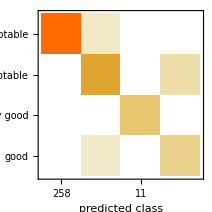
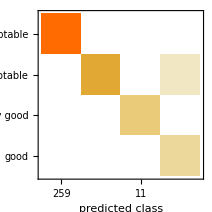
{Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.80.6) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.973 ± 0.013
Mean cross entropy | 0.0273 ± 0.014
Single evaluation time | 6.86 ms/example
Batch evaluation speed | 1.34 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.40.4) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.974 ± 0.014
Mean cross entropy | 0.026 ± 0.015
Single evaluation time | 7.02 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{trainedSoftNet,trainedHardNet}
```

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.99422